```mathematica
(*定义n等分时第i个基函数*)
Clear[basis,uh];
basis[n_,u_,i_,x_]:=Module[{temp1=0,temp2=0},
If[(i-1)/n<x≤i/n,temp1=n n (2 x-(2 i-1)/n) (x-(i-1)/n),
If[i/n<x<(i+1)/n,temp1=n n (2 x-(2 i+1)/n) (x-(i+1)/n),
temp1=0]];
If[(i-1)/n<x<i/n,temp2=4 n n (x-(i-1)/n) (i/n-x),temp2=0];
u[[i]]*temp1+u[[i+n-1]]*temp2
];
```

```mathematica
(*定义离散数值解*)
uh[n_,u_,x_]:=Module[{temp1=0,temp2=0},
temp1=Sum[basis[n,u,i,x],{i,1,n-1}];
If[(n-1)/n<x<n/n,temp2=4 n n (x-(n-1)/n) (n/n-x),temp2=0];
temp1+u[[2 n-1]]*temp2
]
```

```mathematica
(*记录误差*)
error=Table[{0,0,0,0},{i,5}];
imglist=Table[{0,0},{i,5}];
```

```mathematica
(*求解系数*)
For[l=0,l<5,l++,
Clear[n,h,A];
(*离散程度*)
n=2^l*10;
h=1/n;
(*系数矩阵*)
A=Table[0,{i,2 n-1},{j,2 n-1}];
For[k=1,k<n-1,k++,
A[[k,k]]=14/3/h;
A[[k,k+1]]=1/3/h;A[[k+1,k]]=1/3/h;
A[[k,k+n-1]]=-8/3/h;A[[k,k+n]]=-8/3/h;
A[[k+n-1,k]]=-8/3/h;A[[k+n,k]]=-8/3/h;

A[[k+n-1,k+n-1]]=16/3/h;
];
A[[n-1,n-1]]=14/3/h;
A[[n-1,n-1+n-1]]=-8/3/h;A[[n-1,n-1+n]]=-8/3/h;
A[[n-1+n-1,n-1]]=-8/3/h;A[[n-1+n,n-1]]=-8/3/h;

A[[2 n-2,2 n-2]]=16/3/h;A[[2 n-1,2 n-1]]=16/3/h;
(*右侧向量*)
f=Table[0,{i,2 n-1}];
For[k=1,k<n,k++,
f[[k]]=NIntegrate[(-2 Cos[x]+(x-1) Sin[x])*((2 x-(2 k-1) h) (x-(k-1) h)/h/h),{x,(k-1) h,k h}]+NIntegrate[(-2 Cos[x]+(x-1) Sin[x])*((2 x-(2 k+1) h) (x-(k+1) h)/h/h),{x,k h,(k+1) h}];
f[[k+n-1]]=NIntegrate[(-2 Cos[x]+(x-1) Sin[x])*(4 (x-(k-1) h) (k h-x)/h/h),{x,(k-1) h,k h}]
];
f[[2 n-1]]=NIntegrate[(-2 Cos[x]+(x-1) Sin[x])*(4 (x-(n-1) h) (n h-x)/h/h),{x,(n-1) h,n h}];
(*求解方程组*)
u=N[Inverse[A].f];
(*100等分离散求解模最大误差*)
delta=1/100;
real=N[Table[(i delta-1) Sin[i delta],{i,0,100}]];
ns=Table[uh[n,u,i delta],{i,0,100}];
error[[l+1,1]]=Max[Abs[real-ns]];
(*生成相关图像*)
table=Table[{i delta,uh[n,u,i delta]},{i,0,100}];
img=Plot[(x-1) Sin[x],{x,0,1},PlotStyle->ColorData[3,"ColorList"]];
img1=ListPlot[table];
imglist[[l+1,1]]=img1;
imglist[[l+1,2]]=Show[img,img1];
(*64等分复化3点Gauss积分求解L1范数误差*)
delta=1/128;
xi=Table[m delta,{m,0,128}];
error[[l+1,3]]=Sum[5/18 (xi[[i+1]]-xi[[i+1]])*Abs[((xi[[i+1]]+xi[[i]])/2-Sqrt[15]/10 (xi[[i+1]]-xi[[i]])-1) Sin[(xi[[i+1]]+xi[[i]])/2-Sqrt[15]/10 (xi[[i+1]]-xi[[i]])]-uh[n,u,(xi[[i+1]]+xi[[i]])/2-Sqrt[15]/10 (xi[[i+1]]-xi[[i]])]]+4/9 (xi[[i+1]]-xi[[i]])*Abs[((xi[[i+1]]+xi[[i]])/2-1) Sin[(xi[[i+1]]+xi[[i]])/2]-uh[n,u,(xi[[i+1]]+xi[[i]])/2]]+5/18 (xi[[i+1]]-xi[[i]])*Abs[((xi[[i+1]]+xi[[i]])/2+Sqrt[15]/10 (xi[[i+1]]-xi[[i]])-1) Sin[(xi[[i+1]]+xi[[i]])/2+Sqrt[15]/10 (xi[[i+1]]-xi[[i]])]-uh[n,u,(xi[[i+1]]+xi[[i]])/2+Sqrt[15]/10 (xi[[i+1]]-xi[[i]])]],{i,1,128}];
]
```

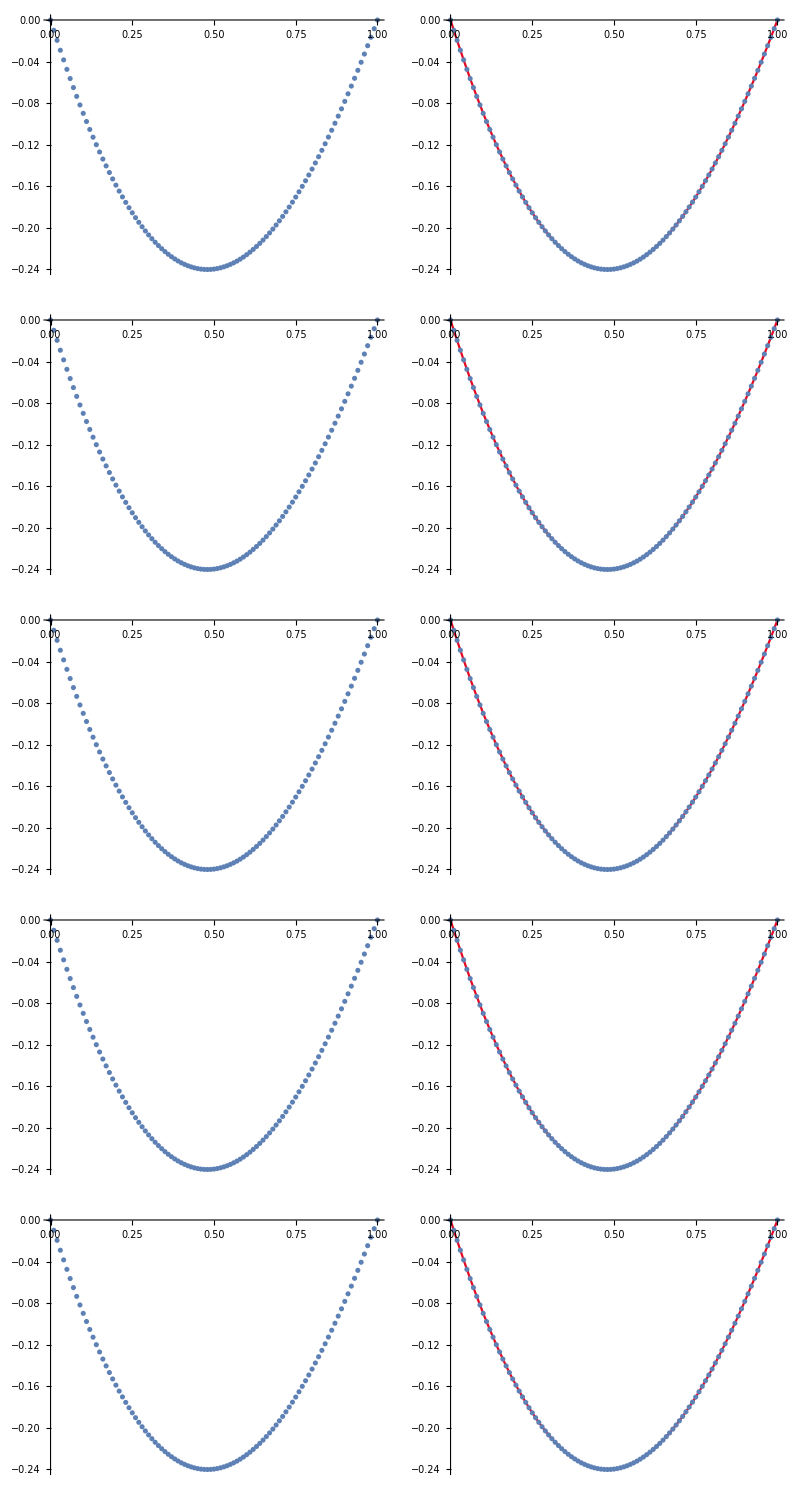

```mathematica
(*依次展示数值求解图像，N=10,20,40,80,160*)
imglist//TableForm
```

```mathematica
(*求收敛阶*)
For[l=2,l≤5,l++,
error[[l,2]]=Log[error[[l-1,1]]/error[[l,1]]]/Log[2];
error[[l,4]]=Log[error[[l-1,3]]/error[[l,3]]]/Log[2]];
list=Table[{10 2^i,error[[i+1,1]],error[[i+1,2]],error[[i+1,3]],error[[i+1,4]]},{i,0,4}];
list[[1,3]]="-";
PrependTo[list,{"n","无穷范数误差","Order","L1范数误差","Order"}];
GridBox[list,ColumnAlignments->Left,GridBoxDividers->{"Rows"->{{True}},"Columns"->{{True}}}]//DisplayForm
```

n | 无穷范数误差 | Order | L1范数误差 | Order
10 | 0.0000193469 | - | 4.36455×10^-6 | 0
20 | 2.47268×10^-6 | 2.96796 | 5.4934×10^-7 | 2.99006
40 | 3.11898×10^-7 | 2.98693 | 6.90573×10^-8 | 2.99183
80 | 3.92172×10^-8 | 2.99151 | 8.84683×10^-9 | 2.96456
160 | 4.83711×10^-9 | 3.01927 | 1.20434×10^-9 | 2.87692